```mathematica
β = 1;
```

```mathematica
eqBase = y[t] y''[t] + β (y[t])^2 y'[t] - (y'[t])^2==0;
```

```mathematica
(*Заметим, что y=const система верна, то есть система находится в состоянии покоя*)
```

```mathematica
systemBase={
y'[t]==v[t],
v'[t] == (v[t])^2/y[t]- β*y[t]*v[t]
};
```

```mathematica
eq1=systemBase[[1]];eq2=systemBase[[2]];
```

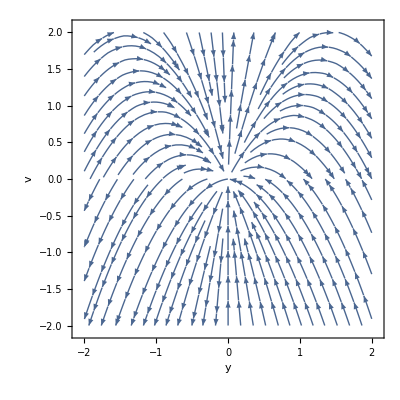

```mathematica
fig1 = StreamPlot[{v, v^2/y-β y v},{y,-2,2},{v,-2,2},Axes-> True, AxesLabel->{"y","v"}]
```

```mathematica
(*Из графика видно, что ситема имеет инфинитное движение при y<0 и v<0, во всех остальных областях предполгаеатся финитное движение)
```

```mathematica
(*Кроме того, видно, что при v=0 система находится в неустойчивом покое, что соответсвует решению ДУ исходного, когда y=const)
```

```mathematica
(*Проаназилиуем поведеление системы в разных оболастях при t->∞ с помощью численного решения*)
```

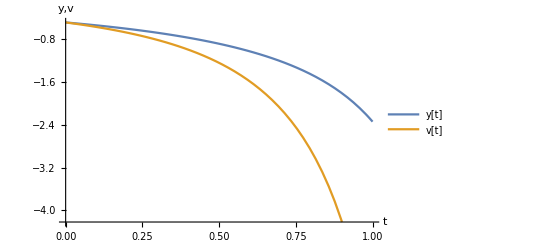

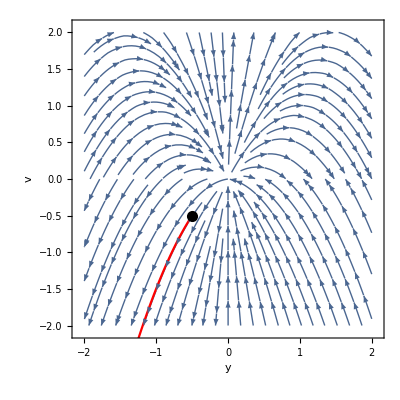

```mathematica
sol1system = NDSolve[{eq1, eq2, y[0]==-1/2, v[0]==-1/2}, {y, v},{t, 0, 1}];
fig1eq1eq2=Plot[{y[t]/.sol1system,v[t]/.sol1system},{t, 0, 1},   AxesLabel->{"t","y,v"}, PlotLegends->{"y[t]","v[t]"}]
fig12eq1eq2 = ParametricPlot[Evaluate[{y[t],v[t]}/.sol1system],{t, 0,1}, PlotRange->{{-2,3},{-2,2}}, PlotStyle->Red, Epilog->{PointSize[0.02], Point[{-1/2, -1/2}]},AxesLabel->{"y","v"}];

fig11 = StreamPlot[{v, v^2/y-β y v},{y,-2,2},{v,-2,2}, Axes-> True, AxesLabel->{y,v},Epilog->{PointSize[0.02], Point[{-1/2, -1/2}]}];
Show[fig11, fig12eq1eq2]
```

```mathematica
(*Уход на бесконечность за бесконеченое время*)
```

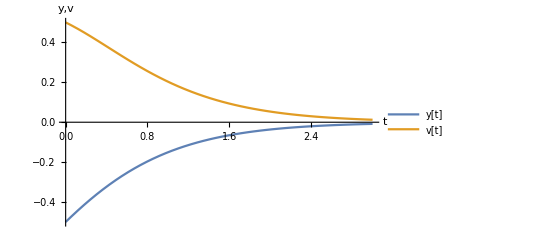

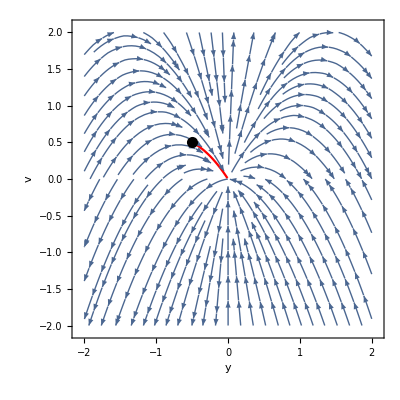

```mathematica
sol2system = NDSolve[{eq1, eq2, y[0]==-1/2, v[0]==1/2}, {y, v},{t, 0, 3}];
fig2eq1eq2=Plot[{y[t]/.sol2system,v[t]/.sol2system},{t, 0, 3},   AxesLabel->{"t","y,v"}, PlotLegends->{"y[t]","v[t]"}]
fig22eq1eq2 = ParametricPlot[Evaluate[{y[t],v[t]}/.sol2system],{t, 0, 3}, PlotRange->{{-1,3},{-2,2}}, PlotStyle->Red, Epilog->{PointSize[0.02], Point[{-1/2, 1/2}]},AxesLabel->{"y","v"}];
fig12 = StreamPlot[{v, v^2/y-β y v},{y,-2,2},{v,-2,2}, Axes-> True, AxesLabel->{y,v},Epilog->{PointSize[0.02], Point[{-1/2, 1/2}]}];

Show[fig12, fig22eq1eq2]
```

```mathematica
(*Приближение к точке за бесконечное время*)
```

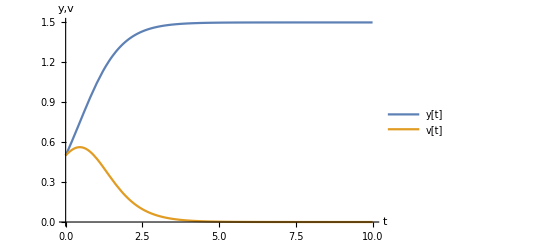

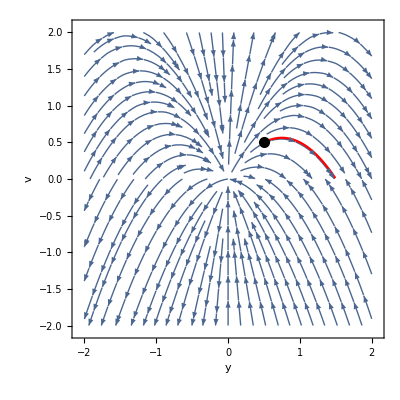

```mathematica
sol3system = NDSolve[{eq1, eq2, y[0]==1/2, v[0]==1/2}, {y, v},{t, 0, 10}];
fig3eq1eq2=Plot[{y[t]/.sol3system,v[t]/.sol3system},{t, 0, 10},   AxesLabel->{"t","y,v"}, PlotLegends->{"y[t]","v[t]"}]
fig32eq1eq2 = ParametricPlot[Evaluate[{y[t],v[t]}/.sol3system],{t, 0, 4}, PlotRange->{{-2,2},{-2,2}}, PlotStyle->Red, Epilog->{PointSize[0.02], Point[{1/2, 1/2}]},AxesLabel->{"y","v"}];
fig13 = StreamPlot[{v, v^2/y-β y v},{y,-2,2},{v,-2,2}, Axes-> True, AxesLabel->{y,v},Epilog->{PointSize[0.02], Point[{1/2, 1/2}]}];
Show[fig13, fig32eq1eq2]
```

```mathematica
(*Уход на константу за конечное время*)
```

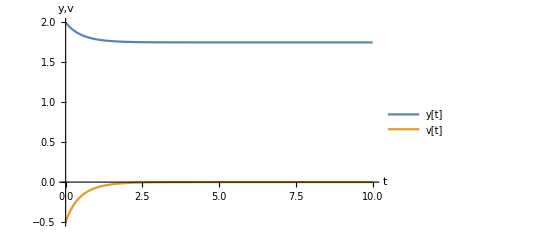

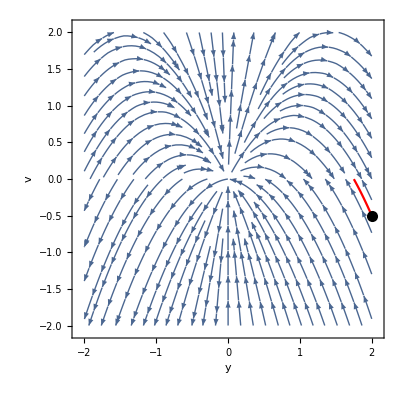

```mathematica
sol4system = NDSolve[{eq1, eq2, y[0]==2, v[0]==-1/2}, {y, v},{t, 0, 10}];
fig4eq1eq2=Plot[{y[t]/.sol4system,v[t]/.sol4system},{t, 0, 10},   AxesLabel->{"t","y,v"}, PlotLegends->{"y[t]","v[t]"}]
fig42eq1eq2 = ParametricPlot[Evaluate[{y[t],v[t]}/.sol4system],{t, 0, 3}, PlotRange->{{-2,2},{-2,2}}, PlotStyle->Red, Epilog->{PointSize[0.02], Point[{2,-1/2}]},AxesLabel->{"y","v"}];
fig14 = StreamPlot[{v, v^2/y-β y v},{y,-2,2},{v,-2,2}, Axes-> True, AxesLabel->{y,v},Epilog->{PointSize[0.02], Point[{2, -1/2}]}];
Show[fig14, fig42eq1eq2]
```

```mathematica
(*Уход на константу за конечное время*)
```

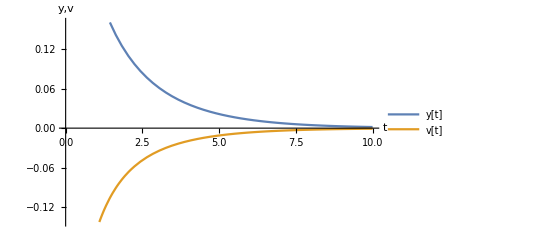

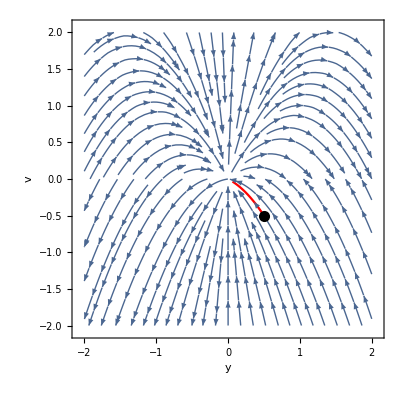

```mathematica
sol5system = NDSolve[{eq1, eq2, y[0]==1/2, v[0]==-1/2}, {y, v},{t, 0, 10}];
fig5eq1eq2=Plot[{y[t]/.sol5system,v[t]/.sol5system},{t, 0, 10},   AxesLabel->{"t","y,v"}, PlotLegends->{"y[t]","v[t]"}]
fig52eq1eq2 = ParametricPlot[Evaluate[{y[t],v[t]}/.sol5system],{t, 0, 3}, PlotRange->{{-2,2},{-2,2}}, PlotStyle->Red, Epilog->{PointSize[0.02], Point[{1/2,-1/2}]},AxesLabel->{"y","v"}];
fig15 = StreamPlot[{v, v^2/y-β y v},{y,-2,2},{v,-2,2}, Axes-> True, AxesLabel->{y,v},Epilog->{PointSize[0.02], Point[{1/2, -1/2}]}];
Show[fig15, fig52eq1eq2]
```

```mathematica
(*Уход на константу за бесконечное время*)
```

```mathematica
DSolve[systemBase, {y[t], v[t]}, t]
```

{{y[t]→1/2 (C[1]+√(C[1]^2 Tanh[1/2 C[1] (t+C[2])]^2)),v[t]→1/4 (C[1]^2-C[1]^2 Tanh[1/2 C[1] (t+C[2])]^2)},{y[t]→1/2 (C[1]-√(C[1]^2 Tanh[1/2 (-t C[1]+C[1] C[2])]^2)),v[t]→1/4 (C[1]^2-C[1]^2 Tanh[1/2 (-t C[1]+C[1] C[2])]^2)}}

```mathematica
(*Решения соответсвуют случаю, где v[t]>0 *)
```

```mathematica
DSolve[{eqBase}, y[t], t]
```

{{y[t]→(ⅇ^(t C[1]+C[1] C[2]) C[1])/(-1+ⅇ^(t C[1]+C[1] C[2]))}}

```mathematica
D[(C1 ⅇ^(C1 t +C2))/(-1+ⅇ^(C1 t +C2)), t]  // Simplify
```

-(C1^2 ⅇ^(C2+C1 t))/((-1+ⅇ^(C2+C1 t))^2)

```mathematica
(*Решение соответсвуют случаю, где v[t]<0 *)
```

```mathematica
(*Аналитическое решение y[t]=(±C1 ⅇ^(C1 t +C1 C2))/(-1±βⅇ^(C1 t +C1 C2)): В зависимости от знакак перед экспонентой различают случаи, где v>0, v<0*)
```

```mathematica
(*v>0*)
```

```mathematica
solVgr0={y[t]->(C1 ⅇ^(C1 t +C2))/(1+ⅇ^(C1 t +C2)),v[t]->(C1^2 ⅇ^(C2+C1 t))/((1+ⅇ^(C2+C1 t))^2)};
```

```mathematica
Solve[{(C1 ⅇ^C2)/(1+ⅇ^C2)==y0,v0==(C1^2 ⅇ^C2)/((1+ⅇ^C2)^2)}, {C1,C2}]
```

{{C1→(v0+y0^2)/y0,C2→ConditionalExpression[2 ⅈ π C[1]+Log[y0^2/v0],C[1]∈Integers]}}

```mathematica
c1c21 = {{C1->(v0+y0^2)/y0,C2->Log[y0^2/v0]}};
```

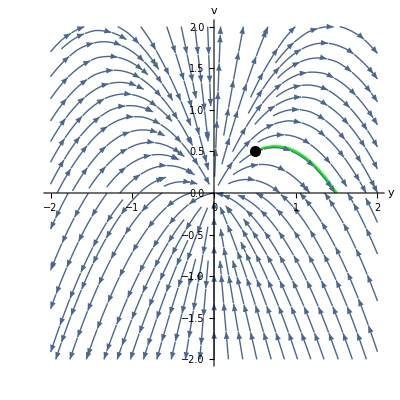

```mathematica
trag11 = ParametricPlot[{y[t], v[t]}/.solVgr0/.c1c21/.{y0-> 1/2, v0-> 1/2}, {t,0,10}, PlotRange->{{-2,2},{-2,2}}, AxesLabel->{y, v}, Epilog->{PointSize[0.02], Point[{1/2, 1/2}]}, PlotStyle->Green];
figtraj1 = StreamPlot[{v, v^2/y-β y v},{y,-2,2},{v,-2,2}, Axes-> True, AxesLabel->{y,v},Epilog->{PointSize[0.02], Point[{1/2, 1/2}]}];
Show[trag11, figtraj1]
```

```mathematica
{y[t], v[t]}/.solVgr0/.c1c21/.{y0-> 1/2, v0-> 1/2}
```

{{(3 ⅇ^(3 t/2))/(4 (1+1/2 ⅇ^(3 t/2))),(9 ⅇ^(3 t/2))/(8 (1+1/2 ⅇ^(3 t/2))^2)}}

```mathematica
(*В 1ой четверти конечная достигается конечное значение за бесконечное время*)
```

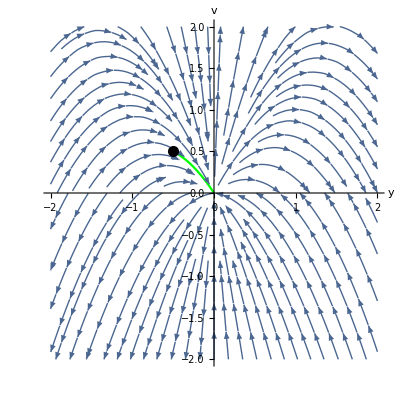

```mathematica
trag11 = ParametricPlot[{y[t], v[t]}/.solVgr0/.c1c21/.{y0-> -1/2, v0-> 1/2}, {t,0,10}, PlotRange->{{-2,2},{-2,2}}, AxesLabel->{y, v}, Epilog->{PointSize[0.02], Point[{-1/2, 1/2}]}, PlotStyle->Green];
figtraj1 = StreamPlot[{v, v^2/y-β y v},{y,-2,2},{v,-2,2}, Axes-> True, AxesLabel->{y,v},Epilog->{PointSize[0.02], Point[{-1/2,1/2}]}];
Show[trag11, figtraj1]
```

```mathematica
{y[t], v[t]}/.solVgr0/.c1c21/.{y0->- 1/2, v0-> 1/2}
```

{{-(3 ⅇ^(-3 t/2))/(4 (1+1/2 ⅇ^(-3 t/2))),(9 ⅇ^(-3 t/2))/(8 (1+1/2 ⅇ^(-3 t/2))^2)}}

```mathematica
(*Во 2ой четверти достигает конечной точки за бесконечное время*)
```

```mathematica
(*v<0*)
```

```mathematica
solLs0={y[t]->(C1 ⅇ^(C1 t +C2))/(-1+ⅇ^(C1 t +C2)),v[t]->-(C1^2 ⅇ^(C2+C1 t))/((-1+ⅇ^(C2+C1 t))^2)};
```

```mathematica
Solve[{(C1 ⅇ^C2)/(-1+ⅇ^C2)==y0,v0==-(C1^2 ⅇ^C2)/((-1+ⅇ^C2)^2)}, {C1,C2}]
```

{{C1→(v0+y0^2)/y0,C2→ConditionalExpression[2 ⅈ π C[1]+Log[-y0^2/v0],C[1]∈Integers]}}

```mathematica
c1c22 = {{C1->(v0+y0^2)/y0,C2->Log[-y0^2/v0]}};
```

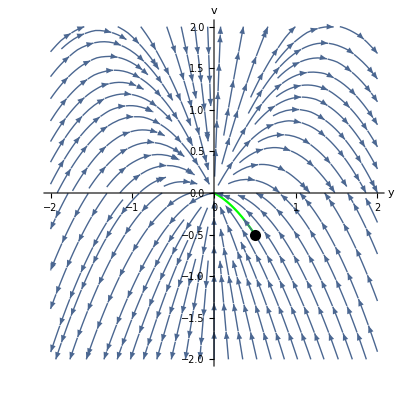

```mathematica
trag12 = ParametricPlot[{y[t], v[t]}/.solLs0/.c1c22/.{y0-> 1/2, v0-> -1/2}, {t,0,10}, PlotRange->{{-2,2},{-2,2}}, AxesLabel->{y, v}, Epilog->{PointSize[0.02], Point[{1/2, -1/2}]}, PlotStyle->Green];
figtraj2 = StreamPlot[{v, v^2/y-β y v},{y,-2,2},{v,-2,2}, Axes-> True, AxesLabel->{y,v},Epilog->{PointSize[0.02], Point[{1/2, -1/2}]}];
Show[trag12, figtraj2]
```

```mathematica
{y[t], v[t]}/.solLs0/.c1c22/.{y0-> 1, v0-> -1/2}
```

{{ⅇ^(t/2)/(-1+2 ⅇ^(t/2)),-ⅇ^(t/2)/(2 (-1+2 ⅇ^(t/2))^2)}}

```mathematica
Solve[-1+2 ⅇ^(t/2)==0,t]
```

```mathematica
(*C1==0 когда v0==-y0^2, при этом же C2==0 => y[t]==не определён, так как происходит деление на 0. Имеем сепаратрису, задаваемую линией v=-y^2*)
```

```mathematica
(*При v0>-y0^2 система уходит на константу, отличную от 0 за бесконечное время (т.к. решается задача Коши, т.е. t>0)*)
```

```mathematica
(*При v0>-y0^2 система уходит на константу за бесконечное время (y->0 при t->∞)*)
```

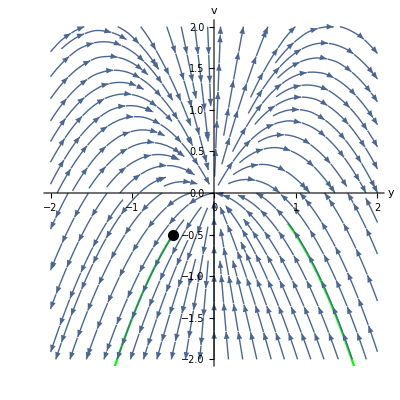

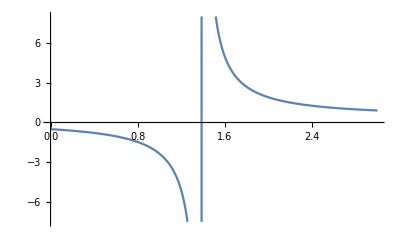

```mathematica
trag12 = ParametricPlot[{y[t], v[t]}/.solLs0/.c1c22/.{y0-> -1/2, v0-> -1/2}, {t,0,3}, PlotRange->{{-2,2},{-2,2}}, AxesLabel->{y, v}, Epilog->{PointSize[0.02], Point[{-1/2, -1/2}]}, PlotStyle->Green];
figtraj2 = StreamPlot[{v, v^2/y-β y v},{y,-2,2},{v,-2,2}, Axes-> True, AxesLabel->{y,v},Epilog->{PointSize[0.02], Point[{-1/2, -1/2}]}];
Show[trag12, figtraj2]
Plot[{y[t]}/.solLs0/.c1c22/.{y0-> -1/2, v0-> -1/2}, {t,0,3}]
```

```mathematica
(*Виден явный уход в бесконечность за конечное время равное t=-C2/C1*)
```